# Hardware Verification Workflow with SCR1

This is demonstration of the project for Wolfram  Hackathon Russia 2018. We developed a driver for SCR1 based on Device Framework. SCR1 is open-source microcontroller core. SCR1 implements RISC-V architecture  (RV32I|E[MC]). Sources to SCR1 is located here:  http://github.com/syntacore/scr1.

This project demonstrates potential application for Wolfram Mathematica to semiconductor industry. It is known that workflow for chips productions is complex.  The most  complicated stage is verification phase. Engineers use expensive toolchain to simulate designs. Here we offer an idea to use comprehensive analytical and visualisation features of Wolfram Mathematica to solve some hardware design tasks. As result we built workflow to introduce Wolfram Mathematica to semiconductor market.

## Features of the workflow

## Architecture

The prototype works with Verilator software (https://www.veripool.org/wiki/verilator). This is open-source free Verilog / System Verilog hardware description language (HDL) simulator. It compiles HDL into C++ code. We wrapped this code with function to communicate with Wolfram Mathematica. On the Wolfram side we wrote simple driver in terms of Wolfram Device Framework. Driver works with C++ code through Wolfram LibraryLink. The full scheme of the prototype is shown below.

```mathematica
TreePlot[{
-Graphics-->"Verilator",
"Verilator"->"C++ model",
"C++ model"->"cpp_bridge",
"cpp_bridge"-> "C++ model",
"cpp_bridge"-> -Graphics-,
-Graphics-->"cpp_bridge"
},Automatic,VertexLabeling->True,DirectedEdges->True]
```

-Graphics-

## Basic Examples

#### Start to work

Initialization
To start working with SCR1 processor it should be loaded SCR1Device package as follows

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SCR1Device`"];
```

Here, we create an instance of SCR1 processor. This is a singleton that’s why it can be created only one instance in one scope.

```mathematica
device = DeviceOpen["SCR1"]
```

DeviceObject[…]

There is a standard way to unload device.

```mathematica
DeviceClose[device]
```

Load program
Reset SCR1 and load program intro the  memory

```mathematica
DeviceExecute[device,
"LOAD",
"./scr1_programs/dhrystone.bin"
];
```

Soft reset SRC1 
This is a reset of SCR1 processor.

```mathematica
DeviceExecute[device,"RESET"];
```

Hard reset SCR1 (soft reset + clean memory and simulator state)

```mathematica
DeviceExecute[device,"HARD_RESET"];
```

#### Read information from SCR1 side

You may read different information when processor works. current state.

SCR1 state
The basic informative function returns assassination with

```mathematica
Dataset@DeviceRead[device,"STATE"]
```

Dataset[<>]

Here State shows current state of the instance (IDLE, WORK, FINISHED). FInished flag  shows 1 if the program is finished otherwise it is false. Clock gives information about number of steps aka clocks so far. IPC, instruction pointer counter, shows an address of current instruction.

SCR1 branch state
The branch state consists of different signals from SCR1 pipeline.

```mathematica
Dataset@DeviceRead[device,"BRANCH"]
```

Dataset[<>]

SCR1 memory bus
It may be implemented an access to any buses. Here is an example for memory data bus.

```mathematica
Dataset@DeviceRead[device,"DBUS"]
```

Dataset[<>]

SCR1 general purpose registers
Registers are basic structure of processor. They reflect the state of processor. Any computations use them for work. We can read the value of them. Here an example of representation values of register in binary and hexadecimal forms.

```mathematica
Dataset@MapIndexed[
{#2[[1]],BaseForm[#1,16],BaseForm[#1,2]}&,
DeviceRead[device,"REGS"]
]
```

Dataset[<>]

Memory
Code of program and data store in the memory. The value is contained at particular address can be read.

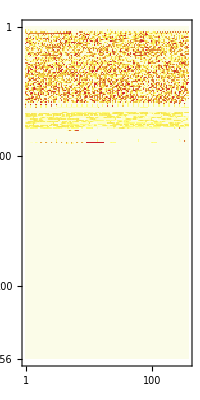

```mathematica
MatrixPlot[
BlockMap[#&,Map[#&,DeviceRead[device,{"MEM",0,32*1024}]],128],
ColorFunction->"TemperatureMap"
]
```

#### Write to SCR1: memory and registers

We can control SR1 by writing some information.

Memory

Here the way to modify memory cell.

```mathematica
DeviceWrite[device,{"MEM",1000,124}]
```

{MEM,1000,124}

Check value into the memory.

```mathematica
DeviceRead[device,{"MEM",1000,1}][[1]]
```

124

General Purpose Registers

```mathematica
DeviceWrite[device,{"REGS",5,30}]
```

{REGS,5,30}

```mathematica
DeviceRead[device,"REGS"][[5]]
```

30

#### SCR1 execution

To start processor working there are several function. The first is “STEP”. This function produces one clock of simulator and returns number of clocks aka steps so far. After finish is reached function doesn’t effect on simulator. The SCR1 has to be reset.

```mathematica
DeviceExecute[device,"STEP"]
```

4

During program execution processor fetches instruction by instruction. Every instruction has an address. Internal IPC registers contains an address of current  instruction. If we want to simulate in per instruction way it should be used the following function. The function returns a value of new IPC.

```mathematica
DeviceExecute[device,"NEXT_IPC"]
```

520

Additionally, SCR1 may be run till a particular IPC value.

```mathematica
DeviceExecute[device,"RUN_UNTIL_IPC",1544]
```

0

If we would like to launch SCR till the end of program execute a “RUN” function.

```mathematica
DeviceExecute[device,"RUN"];
```

If program prints something to display it can be viewed from src1_output.txt file. Standard output stream is redirected to this file.

```mathematica
Framed@Import["src1_output.txt"]
```

HELL0 SCR1

Dhrystone Benchmark, Version 2.1 (Language: C)

Program compiled without 'register' attribute

Execution starts, 500 runs through Dhrystone
Execution ends

Final values of the variables used in the benchmark:

Int_Glob:            5
        should be:   5
Bool_Glob:           1
        should be:   1
Ch_1_Glob:           A
        should be:   A
Ch_2_Glob:           B
        should be:   B
Arr_1_Glob[8]:       7
        should be:   7
Arr_2_Glob[8][7]:    510
        should be:   Number_Of_Runs + 10
Ptr_Glob->
  Ptr_Comp:          11636
        should be:   (implementation-dependent)
  Discr:             0
        should be:   0
  Enum_Comp:         2
        should be:   2
  Int_Comp:          17
        should be:   17
  Str_Comp:          DHRYSTONE PROGRAM, SOME STRING
        should be:   DHRYSTONE PROGRAM, SOME STRING
Next_Ptr_Glob->
  Ptr_Comp:          11636
        should be:   (implementation-dependent), same as above
  Discr:             0
        should be:   0
  Enum_Comp:         1
        should be:   1
  Int_Comp:          18
        should be:   18
  Str_Comp:          DHRYSTONE PROGRAM, SOME STRING
        should be:   DHRYSTONE PROGRAM, SOME STRING
Int_1_Loc:           5
        should be:   5
Int_2_Loc:           13
        should be:   13
Int_3_Loc:           7
        should be:   7
Enum_Loc:            1
        should be:   1
Str_1_Loc:           DHRYSTONE PROGRAM, 1'ST STRING
        should be:   DHRYSTONE PROGRAM, 1'ST STRING
Str_2_Loc:           DHRYSTONE PROGRAM, 2'ND STRING
        should be:   DHRYSTONE PROGRAM, 2'ND STRING

Number_Of_Runs= 500, HZ= 1000000
Time: begin= 18931, end= 234497, diff= 215566
Microseconds for one run through Dhrystone: 431
Dhrystones per Second:                      2319
- tb/scr1_top_tb_axi.sv:314: Verilog $finish

## Additional Examples

#### Develop new devices

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
branchstatelist=Table[
DeviceRead[device,"next_ipc"];
DeviceRead[device,"get_branch_state"],
20000
];
```

```mathematica
jumpsDataset=Select[branchstatelist,(#[[3]]+#[[4]]>0)&];
```

```mathematica
jumpsDataset//TableView
```

1:eJzt2rFLVVEcB/BbTysV1CE0RKTiIRHODeLQECEhEg4N0RQF0VDQ0CDh0CQN
IQ2N0iwhDU7NEeEQDQ0NESHR1F/QEJ3T7aLnh8KDwh72ufB4/D6c873Xy9eH
7+Kp63cX7hyuqurmcFX1pvexPKTjUP32a2aMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYO8jW/m2NZ1vsK9flebVVrltP87NgW2k+2Sr35rkd
1k236tdOm2ptn6PZm+etYFutzq9lJFi+lolg7T3OK0+ePHny5MmTJ0+ePHny
5DV5nX7XnQrrphhj/9z24xnUfjwPmxssLc+dXl+3f8bKkydPnjx58uTJkydP
njzPtBj7n+2gPL/q9Fq6/bNTnjx58g5a3nqwnPch2OyRqlo5Up43z5O9peX5
3Fi5txqvqvPBvqX5YrBPab48Vubl+VZY9yDNa2Fdnt8Hy/NMb7l3vqd+7VyX
548j5bqtE1X1NdjqaLruYCvJ+kdLm0jzldHyHHleDpbnbrpXS+G+5Hkx2KJ7
tee9ethT5uV79SSsy/OrYHnu9Hd1I+zd6LK8t+Ee5Dx//8mTJ0+ePHl/L8+z
XMa6z/7kWem7vnLv8mD67j1U2o00Xwp2O82Pg10drqrnwe4nexFsPNnrYPeS
be6y7nOwpWRfdln3PdijZD92WXd8uLSnw7UXlvadCTaT5ulgc2m+NrQ95yPP
C0fDfUlz+1i5Ls+b4f8s87zWX+6dTXY6/ByTaX7ZX+7N85uw9+xA53vz2p2W
5wsD5d75NE+FvXnWF33RF33RF33Rl3KdvuiLvuiLvtSHvuiLvuhLY/qiL/qi
L43pi77oS33oi77oi740pi/6oi/1oS/6oi/6oi/lOn3RF33RF32pD33RF33R
l8b0RV/0RV8a0xd90Zf60Bd90Rd9aUxf9EVf6kNf9EVf9KUb+vITz4Czhg==

Разбиваем на 2 выборки :

```mathematica
trainingSamples=Round[0.7*Length[jumpsDataset]];
```

Решаем задачу классификации на 2 класса

```mathematica
historyLen=20;
trainingData=Reap[
For[i=historyLen+1,i≤trainingSamples,i++,
Sow[jumpsDataset[[i-historyLen;;i-1,3]]->jumpsDataset[[i,3]]]]
][[2,1]];
classes={0,1};
```

Создаем простую сеть

```mathematica
bpNet=NetChain[
{LinearLayer[10],Ramp,LinearLayer[],SoftmaxLayer[]}
]
```

NetChain[]

Обучаем сеть

```mathematica
trainedNet=NetTrain[bpNet,trainingData,Method->"SGD"]
```

NetChain[]

Подготавливаем тестовую выборку

```mathematica
testData=Reap[
For[i=trainingSamples+1,i≤Length[jumpsDataset],i++,
Sow[jumpsDataset[[i-historyLen;;i-1,3]]->jumpsDataset[[i,3]]]]
][[2,1]];
```

Смотрим метрики

```mathematica
cm=ClassifierMeasurements[trainedNet,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.69579

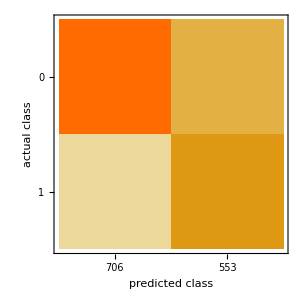

```mathematica
cm["ConfusionMatrixPlot"]
```

#### Work with assembler

```mathematica
asm=Select[Import["./programs/dhrystone21.dump","Lines"],StringLength[#]>0&];
```

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/programs/dhrystone21.hex"
}];
labels=Select[Flatten[#,1]&@StringCases[asm,StartOfString~~Shortest[address:HexadecimalCharacter..]~~" <"~~Shortest[label__]~~">"~~Shortest[__]-> {address,label}],FromDigits[#[[1]],16]≠0&];
labelsHex=Sort[Map[{FromDigits[#[[1]],16],#[[2]]}&,labels],#1[[1]]<#2[[1]]&];
```

```mathematica
ipcList = Table[DeviceRead[device,"next_ipc"],150000];
```

```mathematica
colorLabels=BlockMap[{#[[1]][[2]],#[[1]][[1]],#[[2]][[1]]}&,Sort[labelsHex],2,1];
colorLabels=MapIndexed[Append[#1,ColorData["CMYKColors"][#2[[1]]/Length@colorLabels]]&,colorLabels];
getColor[b_]:=SelectFirst[colorLabels,#[[2]]≤b  && b ≤  #[[3]]&][[4]];
getName[b_]:=SelectFirst[colorLabels,#[[2]]≤b  && b ≤  #[[3]]&][[1]];
dataGraph=Union[
BlockMap[#[[1]]->#[[2]]&,Select[BlockMap[If[Abs[#[[1]]-#[[2]]]>4,#[[1]],0]&,ipcList,2,1 ],#>0&],2,1]
];
```

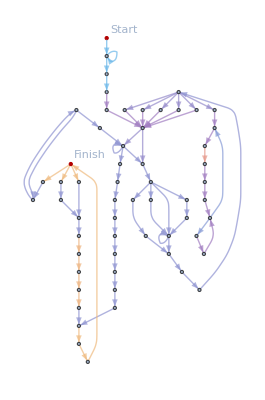

```mathematica
c=HighlightGraph[
dataGraph,
{
Labeled[(First@dataGraph)[[1]],"Start"],Labeled[(Last@dataGraph)[[1]],"Finish"],Map[Style[#,getColor[#[[1]]]]&,dataGraph],
Map[Tooltip[#,getName[#[[1]]]]&,dataGraph]
},
GraphLayout->"LayeredDigraphEmbedding"
]
```

#### Evaluate statistics of memory access

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
busData=Table[
DeviceRead[device,"step"];
DeviceRead[device,"get_data_bus"
],100000];
```

```mathematica
busDataClean=Select[busData,#[[1]]>0 &];
```

```mathematica
busDataCleanFull=Flatten[Map[
Range[
#[[1]],#[[1]]+(#[[2]]-1)
]&,
busDataClean]];
```

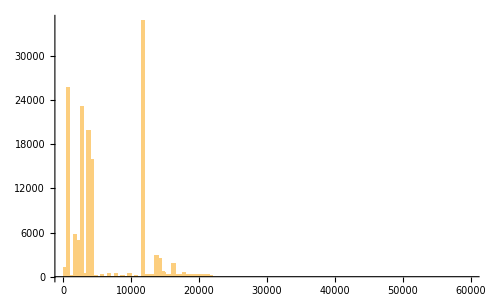

```mathematica
Histogram[busDataCleanFull,{0,60000,500}]
```

#### Execution graph

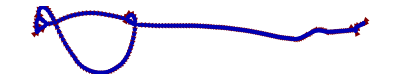

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/scr1_programs/dhrystone.bin"
}];
ipcList = Table[DeviceRead[device,"next_ipc"],10000];g=Union[BlockMap[#[[1]]->#[[2]]&,ipcList,2,1]];
GraphPlot[g,DirectedEdges-> True]
```